```mathematica
dataname=NotebookDirectory[]<>"data.mx"
<<(dataname)
format[num_]:=ToString@NumberForm[num,{3,0},NumberPadding->{"0", ""},NumberSigns->{"", ""}];
f0[num_]:=Module[{},
json=Import[NotebookDirectory[]<>"sample\\"<>format[num]<>".json"];
nns=json[[1]]//Length;
notes=Table[{"note","duration"}/.json[[1]][[i]],{i,1,nns}];
durationsSorted=Sort[Function[x,Round[x[[2]]/40]]/@notes];
durations=Function[x,Min[32,Round[x[[2]]/40]]]/@notes;
features=Function[x,Min[32,Round[x[[2]]/40]]*128+x[[1]]]/@notes;
notes2=Function[x,x[[1]]+1]/@notes;(* add 1 => (1,128) *)
times=Table[Total[durations[[1;;i]]],{i,1,nns}];
notes2
]
Onehot[xs_,n_]:=NumericArray[Table[UnitVector[n,xs[[i]]],{i,1,Length@xs}],"Real32"]
Onehot[{1,2,3,4,5},5]
```

D:\Stuff\Research\MM\mcmusic\data.mx

NumericArray[…]

```mathematica
(*data=TemporalData[{notes2},{times}]*)
If[!FileExistsQ[dataname],
data=Table[f0[i],{i,1,909}];
DumpSave[NotebookDirectory[]<>"data.mx",data];
]
ls=Length/@data;
(* use shortened one-hot encoding *)
{min,max}={Min@(TakeWhile[#,Function[x,x≠1]]&/@data),Max@data}
ndim=max-min+2
embed[n_]:=If[n==1,1,n-min+2];
restore[n_]:=If[n==1,1,n+min-2];
embed/@data[[1]];
data[[1]];
```

{43,99}

58

```mathematica
AllTrue[Table[AllTrue[data[[i]],Function[x,IntegerQ[x]&&1≤x≤128]],{i,1,Length@data}],Identity]
```

True

```mathematica
(*ndim=128*)
counter=0;
splitMelody[mel_]:=Module[{l=Length@mel},
i=RandomInteger[{1,l-2}];
j=RandomInteger[{i+1,l-1}];(* at least one *)
counter=counter+j-i+1;
Onehot[embed/@mel[[i;;j]],ndim]->First@Onehot[embed/@{mel[[j+1]]},ndim]
]
(*trainSet=Table[Onehot[data[[i]],ndim]->Onehot[data[[i]],ndim],{i,1,Length@data}];*)
trainSet=splitMelody/@RandomChoice[data,50000];
validationSet=splitMelody/@RandomChoice[data,1000];
meanLen=counter/(Length[trainSet]+Length[validationSet])//N
(*{Min@samples,Max@samples}*)
```

123.055

```mathematica
net=NetChain[{
LongShortTermMemoryLayer[512,"Input"->{"Varying",ndim}],
ElementwiseLayer["SELU"],
NetMapOperator[BatchNormalizationLayer["Input"->512]],
DropoutLayer[0.3],
LongShortTermMemoryLayer[512,"Input"->{"Varying",512}],
ElementwiseLayer["SELU"],
NetMapOperator[BatchNormalizationLayer["Input"->512]],
DropoutLayer[0.3],
SequenceLastLayer[],
LinearLayer[ndim,"Input"->512],
SoftmaxLayer[]
}];
net=NetInitialize[net,"Method"->"Xavier"]
schedule[b_,bmax_]:=0.65^Floor[b/(bmax/10)];
(*net[samples]//Dimensions*)
```

NetChain[<>]

```mathematica
(* Adding dropout in LSTM gives crash: maybe a cuDNN bug *)
trained=NetTrain[net,trainSet,
TargetDevice->"GPU",
LossFunction->CrossEntropyLossLayer["Probabilities"],
MaxTrainingRounds->200,
BatchSize->48,
Method->{"ADAM",
"LearningRate"->5.*^-4,
"L2Regularization"->1.*^-4,
"LearningRateSchedule"->schedule,
"GradientClipping"->1
},
 TrainingProgressReporting->"Panel",
WorkingPrecision->"Mixed"
]
DumpSave["model2.mx",trained]
```

NetTrain::gpumemex: Computation aborted: GPU memory exhausted.

$Failed

{$Failed}

```mathematica
Internal`$LastInternalFailure
```

Internal`$LastInternalFailure

```mathematica
DumpSave[NotebookDirectory[]<>"model2.mx",trained]
trained[First@Keys@RandomSample[trainSet,1]]
```

{$Failed}

$Failed[First[Keys[RandomSample[trainSet,1]]]]

{66,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

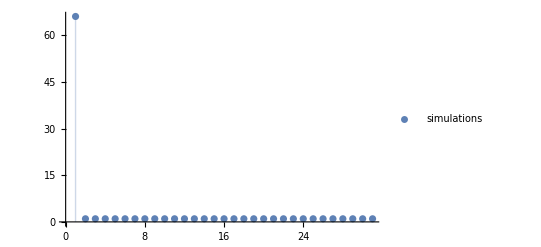

```mathematica
InferenceLSTM[seed_,model_,l_]:=Nest[
Module[{note=Normal@model[#]},
note=First@Ordering[note,-1];
(* note ~ [1, ndim], in-seq ~ [N, ndim] *)
Join[#,Onehot[{note},ndim],1]
]&
,seed,l
]
generation=restore/@Flatten@(Ordering[#,-1]&/@Normal[
InferenceLSTM[Onehot[{RandomInteger[ndim]},ndim],trained, 30]
])
ListPlot[generation,PlotStyle->{Thick,Dashed},
PlotLegends->{"simulations"},Filling->Axis]
```

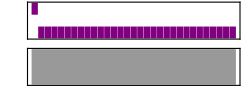

```mathematica
GenChord[x_]:=If[RandomReal[1]>0.5,{x,x+4,x+7},{x,x+3,x+7}]
SaveWave[gen_,instrument_,fn_]:=Module[{l=Length[gen],unit=0.24,shifts={0,-5,5}},
sound=Sound[
Table[
Sound[
If[#!=1,
SoundNote[If[RandomReal[1]>0.85,GenChord[#-64+shifts[[i]]],#-64+shifts[[i]]],unit,instrument],
SoundNote["C",unit,instrument,SoundVolume->0]
]&/@gen,
{0,unit*l}
],
{i,1,1}
]
];
(*EmitSound@sound*)
Export[NotebookDirectory[]<>fn<>".mid",sound];
Export[NotebookDirectory[]<>fn<>".wav",sound];
sound
]
SaveWave[generation,"Piano","lstm\\1"]
```